```mathematica
a=({{-1, 0, 1}, {-2, 1, 1}, {2, 3/2, 1}});
s1[x_]:=a3 x^3+a2 x^2+a1 x+a0;
s2[x_]:=b3 x^3+b2 x^2+b1 x+b0;
```

```mathematica
Solve[{s1[-1]==-2,s1'[-1]==2,s1[0]== 1,s1'[0]== 3/2},{a0,a1,a2,a3}]
```

{{a0→1,a1→3/2,a2→-4,a3→-5/2}}

```mathematica
Solve[{s2[0]==1,s2'[0]==3/2,s2[1]== 1,s2'[1]== 1},{b0,b1,b2,b3}]
```

{{b0→1,b1→3/2,b2→-4,b3→5/2}}

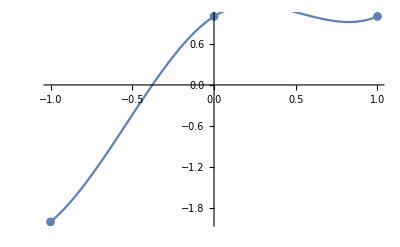

```mathematica
Show[ListPlot[Transpose[a][[All,1;;2]],PlotMarkers->Automatic],
Plot[s1[x]/.Solve[{s1[-1]==-2,s1'[-1]==2,s1[0]== 1,s1'[0]== 3/2},{a0,a1,a2,a3}][[1]],{x,-1,0}],
Plot[
s2[x]/.Solve[{s2[0]==1,s2'[0]==3/2,s2[1]== 1,s2'[1]== 1},{b0,b1,b2,b3}][[1]],{x,0,1}]]
```